Задача сводится заменой y'=y_2, y=y_1 к системе: y_2'=11 y_1 + 10 y_2;    y_1'= 0 y_1+y_2.

```mathematica
f[y1_,y2_]:= 11 y1 + 10y2;
F[t_,{y1_,y2_}]:={y2,f[y1,y2]}; (* такая наша функция правой части ОДУ*)

RungeKutta3[a_,b_,α_,n_,f_]:= (* вводим в параметры функции Р-К: начало отрезка; конец отрезка;  начальное значение y(0); число на которое мы разбиваем отрезок; сама функция правой части ОДУ *)

Module[{h,j,k1,k2,k3,Y,T,R},
h=(b-a)/n;
Y=T=Table[0,{n+1}];
Y[[1]]=α;T[[1]]=a; (* T - сетка отрезка, Y - значения функции y в каждом узле сетки*)
For[j=1,j≤n,++j, (* сам метод  Р-К тут*)
k1=f[T[[j]],Y[[j]]];
k2=f[T[[j]]+h/2,Y[[j]]+k1*h/2];
k3=f[T[[j]]+h,Y[[j]]+(-k1+2 k2)*h];

Y[[j+1]]=Y[[j]]+h/6*(k1+4 k2+k3);
T[[j+1]]=T[[j]]+h;
(* здесь Subscript[с, 1]=0, Subscript[с, 2]=1/2, Subscript[с, 3]=1; Subscript[b, 1]=1/6, Subscript[b, 2]=4/6, Subscript[b, 3]=1/6, Subscript[a, 21]=1/2,  Subscript[a, 31]=-1, Subscript[a, 32]=2, остальные - нули*)
];
R=Table[0,{n+1}];
For[j=1,j≤n+1,j++,R[[j]]=Y[[j]] [[1]] ];

Print[ListPlot[Transpose[{T,R}]]]
];

RungeKutta3[0.,10,{1.,-1.},100,F];
```

-Graphics-

Проверим себя с помощью нормального кода в котором используется встроенная функция:

{y'[x]==z[x],z'[x]==11 y[x]+10 z[x],y[0]==1,z[0]==-1}

{{y[x]→InterpolatingFunction[…][x],z[x]→InterpolatingFunction[…][x]}}

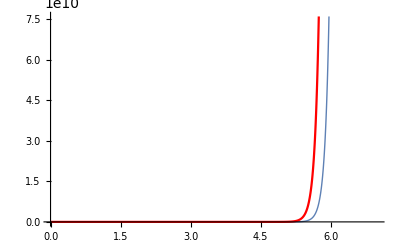

```mathematica
system={y'[x]==z[x],z'[x]==11 y[x]+10z[x],y[0]==1,z[0]==-1}
mma=NDSolve[system,{y[x],z[x]},{x,0,10},Method->"ImplicitRungeKutta" (* просто говорим: используй явный метод Р-К*),"StartingStepSize"->1/5]
Plot[{y[x]/.mma,z[x]/.mma},{x,0,7},PlotStyle->{Thick,Red}]
(* нам нужен красный график *)
```

Сделаем просто нормальное решение, как мы делали бы в обычной жизни:

{{r→InterpolatingFunction[…]}}

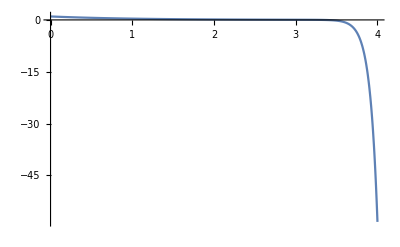

```mathematica
s =NDSolve[{r''[x]-10r'[x]-11r[x]==0,r[0]== 1, r'[0]==-1}, r, {x,0,4}]
Plot[Evaluate[r[x]/.s],{x,0,4},PlotRange->All]
```